# The Madelung Energy of an Ionic Crystal

Terry Cevallos, Milagros Delgado, Daheny López, Quray Potosí, and Ángel Salazar
School of Physical Sciences and Nanotechnology, Yachay Tech University, Urcuquí - Ecuador

## 2D Lattice

Consider a 2D lattice from a rock-salt crystal (called bipartite lattice). Obtain the Madelung (electrostatic) energy and show how the calculation is sensitive to the way in which the infinite sum is truncated (squares or circles).

```mathematica
(*i+j -> interactions between positive or negative charges.*)
(*Energy when 2 charges are at the same position -> approaches to ∞.*)
```

```mathematica
sqSum[n_]:=Sum[If[i==j==0,0,N[(-1)^(i+j)/(√(i^2+j^2))]],{i,-n,n},{j,-n,n}] (*If i = j (particles are at the same position), the energy is 0.*)
```

(∨ is EscorEsc)

```mathematica
crSum[n_]:=Sum[If[√(i^2+j^2)>n ∨ i==j==0,0,N[(-1)^(i+j)/(√(i^2+j^2))]],{i,-n,n},{j,-n,n}]
```

```mathematica
(*The sum has to converge, since the energy of a ionic crystal is finite.*)
(*This is the formula to compute the Coulombic energy of an arangement of charges distributed in a crystal (infinite in all directions).*)
```

Let’s understand what is doing sqSum[n]:

```mathematica
sqSum[1]
```

-1.17157

```mathematica
Table[If[i==j,0,f[i,j]],{i,-1,1},{j,-1,1}]//Flatten
```

{0,f[-1,0],f[-1,1],f[0,-1],0,f[0,1],f[1,-1],f[1,0],0}

```mathematica
N[(-1)^(i+j)/(√(i^2+j^2))]/.{i->-1,j->-1}
```

0.707107

```mathematica
N[(-1)^(i+j)/(√(i^2+j^2))]/.{i->-1,j->0}
```

-1.

```mathematica
N[(-1)^(i+j)/(√(i^2+j^2))]/.{i->-1,j->1}
```

0.707107

```mathematica
N[(-1)^(i+j)/(√(i^2+j^2))]/.{i->0,j->-1}
```

-1.

```mathematica
N[(-1)^(i+j)/(√(i^2+j^2))]/.{i->0,j->0} (*This case we made 0 with the if statement.*)
```

Power::infy: Infinite expression 1/(√0) encountered.

ComplexInfinity

```mathematica
N[(-1)^(i+j)/(√(i^2+j^2))]/.{i->0,j->1}
```

-1.

```mathematica
N[(-1)^(i+j)/(√(i^2+j^2))]/.{i->1,j->-1}
```

0.707107

```mathematica
N[(-1)^(i+j)/(√(i^2+j^2))]/.{i->1,j->0}
```

-1.

```mathematica
N[(-1)^(i+j)/(√(i^2+j^2))]/.{i->1,j->1}
```

0.707107

```mathematica
(*What we did here is to debug what we want to do with the sqSUm[_n] function.*)
```

```mathematica
4 +4  (*We got 4 times 0.71 and 4 times -1.*)
```

-1.17157

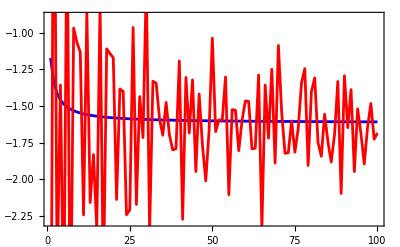

```mathematica
DiscretePlot[
{sqSum[n], crSum[n]}, {n,1,100},
Filling->None,
Frame->True,
Joined->True,
PlotStyle->{Blue, Red}
]
```

```mathematica
(*To get the data points, double click 3 times over the blue line and copy it.*)
(*Blue (circle sum) -> clear convergence (we're gonna use it from now).*)
(*Why the red line is so irregular? It's an artifact; we know that crystals have a finite energy, but how we compute that energy is other hisotry (better ways than others). Each line here represents an algorithm. The red line repreents a very unstable algorithm.*)
(*Why the algorithm with circles converges faster than the algorithm with squares?*)
```

```mathematica
data=-Graphics-
```

-Graphics-

```mathematica
line=data[[1,4,4,1,1]];
```

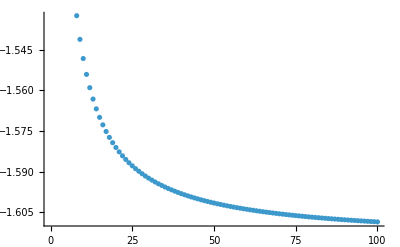

```mathematica
line//ListPlot
```

### Model 1

```mathematica
model1=c[1]+c[2]Exp[-c[3] x]+c[4] x^(-c[5]);
```

```mathematica
nlm1=NonlinearModelFit[line,model1,Table[c[n],{n,5}],x]
```

FittedModel[…]

```mathematica
nlm1[x]
```

-1.61699-0.797536 ⅇ^(-1.87376 x)+0.567911/x^0.919467

```mathematica
nlm1["RSquared"]//NumberForm[#,16]&
```

0.999999970625266

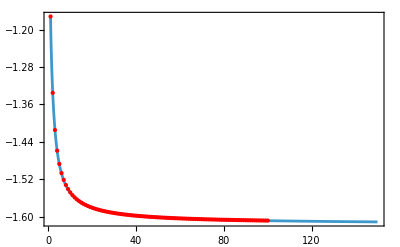

```mathematica
Plot[nlm1[x],{x,1,150},
Frame->True,
Epilog->{Red,Point[line]},
PlotRange->All
]
```

```mathematica
Limit[nlm1[x],x->∞]
```

-1.61699

### Model 2

```mathematica
model2=c[1]+c[2]Exp[-c[3]/x];
```

```mathematica
nlm2=NonlinearModelFit[line,model2,Table[c[n],{n,3}],x]
```

FittedModel[…]

```mathematica
nlm2[x]
```

-0.924787-0.690899 ⅇ^(-1.03194/x)

```mathematica
nlm2["RSquared"]//NumberForm[#,16]&
```

0.999999974427625

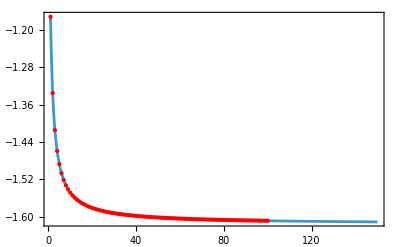

```mathematica
Plot[nlm2[x],{x,1,150},
Frame->True,
Epilog->{Red,Point[line]},
PlotRange->All
]
```

```mathematica
Limit[nlm2[x],x->∞]
```

-1.61569

```mathematica
(*This model is better, since we have almost the same R value, but we have only 3 variables.*)
```

## 3D Lattice: The NaCl Crystal

Now let’s evaluate the Madelung energy for the NaCl crystal, considering that r0 = 2.81 Å (from experiments). The experimental value of the cohesion energy is -7.9 eV/atom.

```mathematica
sqSum[n_]:=Sum[If[i==j==k==0,0,N[(-1)^(i+j+k)/(√(i^2+j^2+k^2))]],{i,-n,n},{j,-n,n},{k,-n,n}]
```

```mathematica
crSum[n_]:=Sum[If[√(i^2+j^2+k^2)>n ∨ i==j==k==0,0,N[(-1)^(i+j+k)/(√(i^2+j^2+k^2))]],{i,-n,n},{j,-n,n},{k,-n,n}]
```

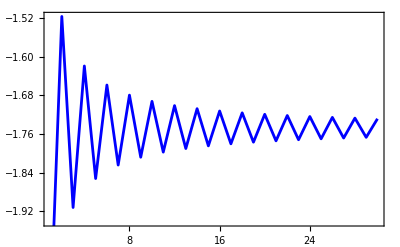

```mathematica
DiscretePlot[
{sqSum[n]}, {n,1,30},
Filling->None,
Frame->True,
Joined->True,
PlotStyle->Blue
]
```

```mathematica
data=-Graphics-
```

-Graphics-

```mathematica
line=data[[1,4,4,1,1]]
```

{{1.,-2.13352},{2.,-1.51665},{3.,-1.9125},{4.,-1.61927},{5.,-1.85254},{6.,-1.65874},{7.,-1.82454},{8.,-1.67964},{9.,-1.80834},{10.,-1.69258},{11.,-1.79777},{12.,-1.70138},{13.,-1.79033},{14.,-1.70775},{15.,-1.78481},{16.,-1.71257},{17.,-1.78056},{18.,-1.71636},{19.,-1.77717},{20.,-1.7194},{21.,-1.77442},{22.,-1.7219},{23.,-1.77213},{24.,-1.724},{25.,-1.77021},{26.,-1.72578},{27.,-1.76856},{28.,-1.72731},{29.,-1.76714},{30.,-1.72864}}

```mathematica
linea=data[[1,4,4,1,1]][[2;;30;;2]]
```

{{2.,-1.51665},{4.,-1.61927},{6.,-1.65874},{8.,-1.67964},{10.,-1.69258},{12.,-1.70138},{14.,-1.70775},{16.,-1.71257},{18.,-1.71636},{20.,-1.7194},{22.,-1.7219},{24.,-1.724},{26.,-1.72578},{28.,-1.72731},{30.,-1.72864}}

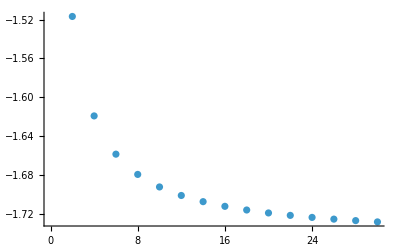

```mathematica
linea//ListPlot
```

```mathematica
lineb=data[[1,4,4,1,1]][[1;;30;;2]]
```

{{1.,-2.13352},{3.,-1.9125},{5.,-1.85254},{7.,-1.82454},{9.,-1.80834},{11.,-1.79777},{13.,-1.79033},{15.,-1.78481},{17.,-1.78056},{19.,-1.77717},{21.,-1.77442},{23.,-1.77213},{25.,-1.77021},{27.,-1.76856},{29.,-1.76714}}

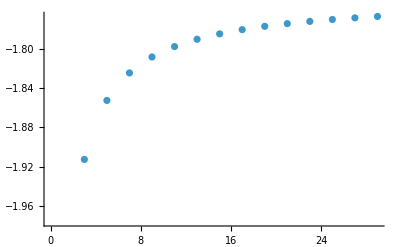

```mathematica
lineb//ListPlot
```

### Model 1

```mathematica
model1=c[1]+c[2]Cos[c[3] x^c[4]]Exp[-c[5]x];
```

```mathematica
nlm1=NonlinearModelFit[line,model1,Table[c[n],{n,5}],x]
```

FittedModel[…]

```mathematica
nlm1[x]
```

-1.74892+0.439448 ⅇ^(-0.128775 x) Cos[2.704 x^1.04839]

```mathematica
nlm1["RSquared"]//NumberForm[#,16]&
```

0.999946772807275

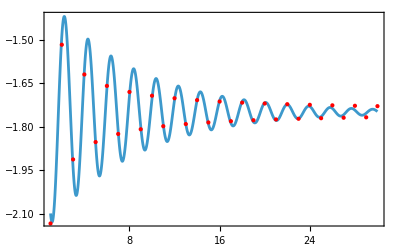

```mathematica
Plot[nlm1[x],{x,1,30},
Frame->True,
Epilog->{Red,Point[line]},
PlotRange->All
]
```

```mathematica
Limit[nlm1[x],x->∞]
```

-1.74892

### Model 2

```mathematica
nlma=NonlinearModelFit[linea,c[1]+c[2]Exp[-c[3]/x],Table[c[i],{i,3}],x]
```

FittedModel[…]

```mathematica
nlmb=NonlinearModelFit[lineb,c[1]+c[2]Exp[-c[3]/x],Table[c[i],{i,3}],x]
```

FittedModel[…]

```mathematica
nlma["RSquared"]//NumberForm[#,16]&
```

0.999999999401422

```mathematica
nlma[x]
```

-1.1085-0.638893 ⅇ^(-0.896129/x)

```mathematica
nlmb["RSquared"]//NumberForm[#,16]&
```

0.9999999911306

```mathematica
nlmb[x]
```

-2.43539+0.687311 ⅇ^(-0.822665/x)

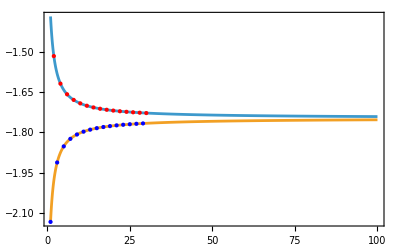

```mathematica
Plot[{nlma[x],nlmb[x]},{x,1,100},
Frame->True,
Epilog->{{Red,Point[linea]},{Blue,Point[lineb]}},
PlotRange->All
]
```

```mathematica
limita=Limit[nlma[x],x->∞]
```

-1.74739

```mathematica
limitb=Limit[nlmb[x],x->∞]
```

-1.74808

```mathematica
limit=(limita+limitb)/2
```

-1.74774

Vacuum permitivity

WolframAlphaQueryResults

```mathematica
um=q^2/(4 π ϵ0 r0) limit 1/(1.6 10^-19)/.{q->1.6 10^-19,ϵ0->8.8541 10^-12,r0->2.81 10^-10} (*Madelung energy approximation in eV.*)
```

-8.94407

```mathematica
(expv-um)/expv 100/.expv->-7.9 (*Error in percentage.*)
```

-13.2161

```mathematica
(*Discuss why do we get this error (we need QM to explain it, but here we used only CM).*)
(*Upload the NB until today's midnight.*)
```